```mathematica
(* equazione di diffusione unidimensionale *)
```

```mathematica
lambda= 0.12;
```

```mathematica
calsp = 0.113 ;
```

```mathematica
dens= 7.8;
```

```mathematica
cost = lambda/(calsp*dens);
```

```mathematica
pde = D[T[x,t],t]==cost D[T[x,t],x,x]
```

T^(0,1)[x,t]==0.136147 T^(2,0)[x,t]

```mathematica
(* risolviamola in un intervallo limitato con con T(0)=T(L)=0 e T(x,0) = T0 = costante *)
```

```mathematica
inifunc1[x_,L_,T0_] = Piecewise[{{0, x==0},{0, x==L}}, T0];
```

```mathematica
Sol[L_,u0_]:=Module[{},NDSolve[{pde, T[x,0]== inifunc1[x,L,u0],T[0,t]==0,T[L,t]==0},T[x,t],{x,0,L},{t,0,9000.0},MaxStepSize->1][[1,1,2]]];
```

```mathematica
nsol[x_,t_]=Sol[100,100]
```

InterpolatingFunction[{{0.,100.},{0.,9000.}},<>][x,t]

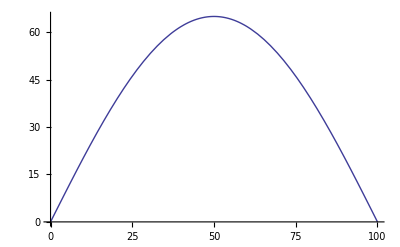

```mathematica
Plot[nsol[x,5000],{x,0,100}]
```

```mathematica
Plot3D[nsol[x,t], {x,0,100},{t,0,10000},PlotRange-> {0,120},AxesLabel->{x,t}]
```

-Graphics3D-

```mathematica
tbl2expF=Table[nsol[x,5000],{x,0, 100, 1}] ;
```

```mathematica
Export["/Users/demichel/TEMPO_DET/DIDATTICA/FISICA_COMPUTAZ_2012/LEZIONI_PRA/DIFF_EQ_E_FOURIER/fourierM.dat",tbl2expF,"Data"];
```

```mathematica
(* PARETE DI UNA CASA: risolviamola in un intervallo limitato con con T(0)=20 T(L)=-5 e T(x,0) = -5 = costante *)
```

```mathematica
lambda= 0.19; (* W/mK POROTON *)
```

```mathematica
calsp = 1000 ; (* J/ Kg K POROTON (www.poroton.it) *)
```

```mathematica
dens= 600; (* kg/m^3 POROTON *)
```

```mathematica
cost = lambda/(calsp*dens);
```

```mathematica
pde = D[T[x,t],t]==cost D[T[x,t],x,x]
```

T^(0,1)[x,t]==3.16667×10^-7 T^(2,0)[x,t]

```mathematica
inifunc2[x_,L_,Tamb_,Texte_] = Piecewise[{{Tamb, x==0},{Texte, x==L}}, Texte];
```

```mathematica
Sol2[L_,Tamb_,Text_]:=Module[{},NDSolve[{pde, T[x,0]== inifunc2[x,L,Tamb,Text],T[0,t]==Tamb,T[L,t]==Text},T[x,t],{x,0,L},{t,0,500000.0}][[1,1,2]]];
```

```mathematica
nsol[x_,t_]=Sol2[0.40,20,-5]
```

InterpolatingFunction[{{0.,0.4},{0.,500000.}},<>][x,t]

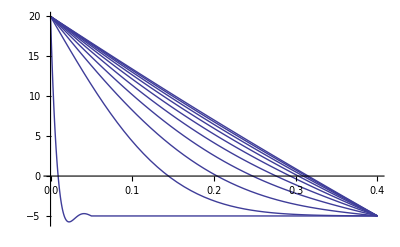

```mathematica
Plot[Table[nsol[x,n],{n,1,200000,20000}],{x,0,0.40},PlotRange->All]
```

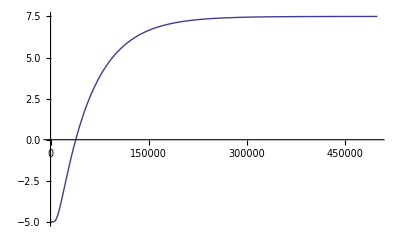

```mathematica
Plot[nsol[0.20,t],{t,0,500000},PlotRange->All]
```

```mathematica
200000/3600//N
```

55.5556

```mathematica
774/5//N
```

154.8

```mathematica
1/0.071125
```

14.0598

```mathematica
lambda1= 0.22;
```

```mathematica
calsp1 = 1000 ;
```

```mathematica
dens1= 600;
```

```mathematica
cost1 = lambda1/(calsp1*dens1);
```

```mathematica
lambda2= 0.037;
```

```mathematica
calsp2 = 1000 ;
```

```mathematica
dens2= 600;
```

```mathematica
cost2 = lambda2/(calsp2*dens2);
```

```mathematica
(*DD[x_,L1_,cost1_,cost2_,dx_] := cost1 + 0.5(1+Tanh[100(x-L1)]) (cost2-cost1)*)
```

```mathematica
DD[x_,L1_,cost1_,cost2_,dx_]:= Piecewise[{{cost1,x-L1<-dx},{cost1+(cost2-cost1)(0.5+1/(2dx)(x-L1)),Abs[x-L1]< dx }},cost2] ;
```

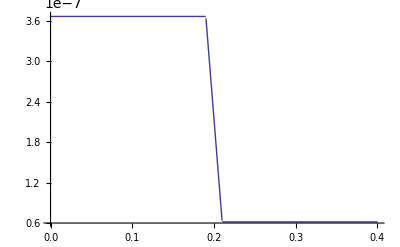

```mathematica
Plot[DD[x,0.2,cost1,cost2,dxmax],{x,0,0.4}]
```

```mathematica
DerDD[x_,L1_,cost1_,cost2_,dx_]=D[DD[x,L1,cost1,cost2,dx],x] ;
```

```mathematica
dxmax=0.001
```

0.001

```mathematica
pdeDW= D[T[x,t],t]==DD[x,L1,cost1,cost2,dxmax] D[T[x,t],x,x]+ D[T[x,t],x] DerDD[x,L1,cost1,cost2,dxmax] /. L1->0.30;
```

```mathematica
pdeDW
```

T^(0,1)[x,t]==(Piecewise[{{0, -0.299+x<0}, {-0.0001525, 0.001-Abs[-0.3+x]>0}, {0, True}}]) T^(1,0)[x,t]+(Piecewise[{{3.66667×10^-7, -0.3+x<-0.001}, {3.66667×10^-7-3.05×10^-7 (0.5+500. (-0.3+x)), Abs[-0.3+x]<0.001}, {6.16667×10^-8, True}}]) T^(2,0)[x,t]

```mathematica
inifuncDW[x_,L_,Tamb_,Texte_] = Piecewise[{{Tamb, x==0},{Texte, x==L}}, Texte];
```

```mathematica
SolDW[L_,Tamb_,Text_]:=Module[{},NDSolve[{pdeDW, T[x,0]== inifuncDW[x,L,Tamb,Text],T[0,t]==Tamb,T[L,t]==Text},T[x,t],{x,0,L},{t,0,500000.0}, Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->2000}}][[1,1,2]]];
```

```mathematica
nsolDW [x_,t_]= SolDW[0.36,20,-5]
```

InterpolatingFunction[{{0.,0.36},{0.,500000.}},<>][x,t]

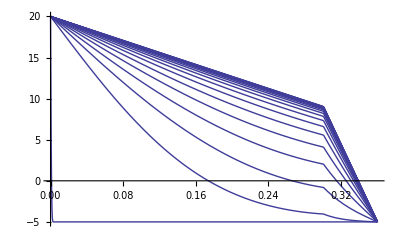

```mathematica
Plot[Table[nsolDW[x,n],{n,1,500000,25000}],{x,0,0.36},PlotRange->All]
```